# Mérés címe

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{bm}"}];(*a kapcsos zárójelbe jönnek az include-álandó latex packagek vesszővel elválasztva, idézőjelek között*)
<<JLink`;InstallJava[];ReinstallJava[JVMArguments->"-Xmx1024m"]; 
Button["Start AutoSave",ScheduledTask[NotebookSave[EvaluationNotebook[]],60]](*ez a sor majd akkor kell ha a sablont elmentetted addig ki van kommentelve*)
<<LabDataProcess`
(*mathematica aktiválásához keygen: ibug.io/blog/2019/05/mathematica-keygen/*)
(*MaTeX package telepítéséhez: http://szhorvat.net/pelican/latex-typesetting-in-mathematica.html*)
```

Start AutoSave

```mathematica
Checkbox[x]
```

Checkbox[x]

## A kiértékelések előtt

```mathematica
ExtractArchive[FindFile["adatok.rar"]](*ez a sor kicsomagol bármilyen tömörített file-t*)
```

```mathematica
CsvMagic["/Users/herman/Downloads/Monte Carlo/NHF/hatask.txt",".txt"," ","mc.xlsx",0](* ez a már sokat használt adatokat excelbe berakó függvény, célszerű a külömböző mérési feladatokat külömböző mappákba rakni és belőlük külömböző exceleket létrehozni*)
```

proba1.xlsx

```mathematica
Separatorinator["/Users/szaszbence/Downloads/SmFeB/Bence/22.03.30","","	",";",".csv"](* Ezzel ki tudod egy mappában cserélni az adott file elválasztó jeleit. Ha már van olyan mappa amit létre akar hozni akkor nem fut le!!!*)
```

## Gyakran használt függvények

## Adatok ábrázolása

```mathematica
data={{{2,3},{1,3}},{{2,5},{1,4}}}
```

{{{2,3},{1,3}},{{2,5},{1,4}}}

```mathematica
{{{2,3},{1,3}},{{2,5},{1,4}}}
```

{{{2,3},{1,3}},{{2,5},{1,4}}}

```mathematica
ClearAll[data]
```

```mathematica
data[[1]]
```

{{2,3},{1,3}}

```mathematica
datas=MultiPlotDataMaker[colx_,coly_,path_,{sheets}]
```

### hibák ábrázolásához

```mathematica
dataserr=Around[data,hiba] (*ha minden x, y adatnak konstans hibája van*)
```

```mathematica
dataxhiba=Partition[Riffle[Around[Flatten[data][[1;;;;2]],hiba],Flatten[data][[2;;;;2]]],2]
datayhiba=Partition[Riffle[Flatten[data][[1;;;;2]],Around[Flatten[data][[2;;;;2]],hiba]],2]
```

```mathematica
datasxhiba=Partition[Riffle[Around[Flatten[data[[#]]][[1;;;;2]],hiba],Flatten[data[[#]]][[2;;;;2]]],2]&/@Range[Length[data]]
```

```mathematica
datasyhiba=Partition[Riffle[Flatten[data[[#]]][[1;;;;2]],Around[Flatten[data[[#]]][[2;;;;2]],hiba]],2]&/@Range[Length[data]]
```

{{{2,3hiba},{1,3hiba}},{{2,5hiba},{1,4hiba}}}

```mathematica
Length[data]
```

2

### ábárzolás

```mathematica
MultiPlot[datas,{"xtengely","ytengely"},{"a adatsor","b adatsor"}]
```

```mathematica
SpeedGrapher[xlsname_,xax_,yax_,{"xtengely","ytengely"}]
```

## Görbe illesztés

```mathematica
f=a*Sqrt[x+c]^-1+b;(*ez csak egy példa bármi lehet a függvény*)
co={{a,10},{b,-10},{c,-100}};(*illesztendő állandók a kezdő értékkel eggyütt, az nem feltétlen kell, lehet csak szimplán így is: {a,b,c}*)
vars=x;
rng={x,xmin,xmax};
FittingAutomaton[data,f,co,vars,rng,{"xtengely","ytengely"},{"a adatsor","b adatsor"}]
```

#### hibával

```mathematica
error=0.1
```

```mathematica
errors=ConstantArray[error,Length[data]]
xhiba={0.2,0.2,0.1}(*ha x nek van hibája y-nak nincs: yhiba=ConstantArray[0,Length[xhiba]], amúgy elég csak yhiba*)
yhiba={0.1,0.1,0.4}
```

```mathematica
errors=RootMeanSquare[#]&/@Partition[Riffle[xhiba,yhiba],2]
```

```mathematica
nlm=NonlinearModelFit[data,f,co,vars,MaxIterations->1000000,Weights->1/errors^2];

lp=ListPlot[data,Frame->True, PlotRange->All,PlotTheme->"Detailed",FrameLabel->MaTeX@{"xtengely","ytengely"},
PlotLegends->SwatchLegend[{ColorData[97,"ColorList"][[1]],Red},
MaTeX@{"adatsor","illesztés"},LegendFunction->ShadowBox],
Joined->False,  Epilog->First@Plot[nlm[x],rng,PlotStyle->Red]]

Print[nlm[{"BestFit","ParameterTable"}]];
```

## Mérés kiértékelése

```mathematica
path="/Users/szaszbence/Downloads/proba1.xlsx";
sheetref =3 ;
colref = 2;
sheetlamb =3;
collamb = 1;
```

```mathematica
rint=Rest[ToExpression[Import[path,{"Data",sheetref,All,colref}]]];
hul=Rest[ToExpression[Import[path,{"Data",sheetlamb,All,collamb}]]];
data=Partition[Riffle[hul,rint],2];
```

```mathematica
Length[data]
```

2000

```mathematica
sr=0.05 (*sample rate, reciprocal of timestep*)
inc=sr/Length[data](*increment*)
freq=Table[f,{f,0,sr-inc,inc}];
```

0.05

0.0000357143

```mathematica
10^{-12}
```

{1/1000000000000}

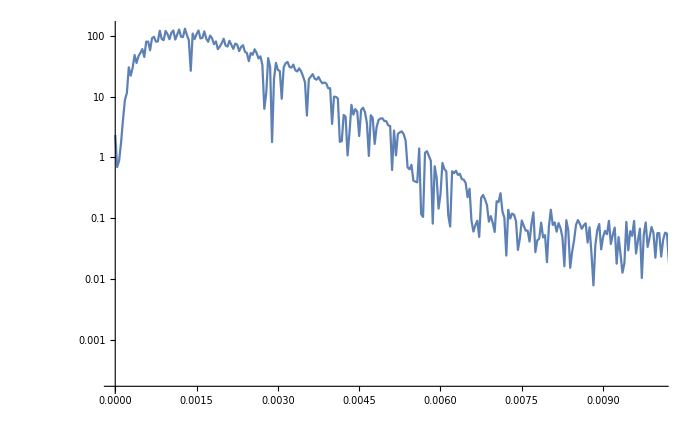

```mathematica
ListLogPlot[Transpose[{freq,Abs[Fourier[rint]]}],PlotRange->{{0.,0.01},All},Joined->True]
```